```mathematica
({{0, 1, 2, 0, 1, 2, 0, 1, 2}, {0, 0, 0, 1, 1, 1, 2, 2, 2}})
```

{{0,1,2,0,1,2,0,1,2},{0,0,0,1,1,1,2,2,2}}

```mathematica
Flatten[Table[Table[{i, j}, {i, 0, 2}], {j, 0, 2}],1]ᵀ//MatrixForm
```

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
0 | 0 | 0 | 1 | 1 | 1 | 2 | 2 | 2)

```mathematica
M=Flatten[Table[Table[{i, j}, {i, 0, 2}], {j, 0, 2}],1];M//MatrixForm
```

(0 | 0
1 | 0
2 | 0
0 | 1
1 | 1
2 | 1
0 | 2
1 | 2
2 | 2)

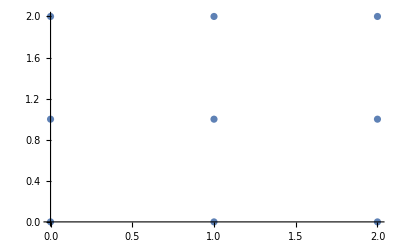

```mathematica
ListPlot[M]
```

```mathematica
A=({{1, 0}, {0, 1}});
```

```mathematica
A.Mᵀ//MatrixForm
```

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
0 | 0 | 0 | 1 | 1 | 1 | 2 | 2 | 2)

```mathematica
ListPlot[(A.Mᵀ)ᵀ]
```

-Graphics-

```mathematica
Subscript[v, 1][a_,b_]:=Norm[{a,b}]({{a}, {b}});
```

```mathematica
Subscript[v, 2][a_,b_]:=Norm[{a,b}]({{a}, {b}});
```

```mathematica
A[u1_,u2_,λ1_,λ2_]:=ArrayFlatten[({{{Normalize[u1ᵀ⟦1⟧]}ᵀ, {Normalize[u2ᵀ⟦1⟧]}ᵀ}})].({{λ1, 0}, {0, λ2}}).Inverse[ArrayFlatten[({{{Normalize[u1ᵀ⟦1⟧]}ᵀ, {Normalize[u2ᵀ⟦1⟧]}ᵀ}})]]
```

```mathematica
A[({{1}, {0}}),({{0}, {1}}),3, 4]//MatrixForm
```

(3 | 0
0 | 4)

```mathematica
Manipulate[Row[{A[({{x1}, {y1}}),({{x2}, {y2}}),λ1, λ2]//MatrixForm,ListPlot[(A[({{x1}, {y1}}),({{x2}, {y2}}),λ1, λ2].Mᵀ)ᵀ,ImageSize->Medium]}], {{x1, 1},-10,10,1},{{y1, 0},-10,10,1},{{x2, 0},-10,10,1},{{y2, 1},-10,10,1},{{λ1, 1},-10,10,1},{{λ2, 1},-10,10,1}]
```

ListPlot::lpn: Transpose[A[{{-8.},{-2.}},{{4.},{8.}},4.,-4.].Transpose[M]] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[A[({{x1}, {y1}}),({{x2}, {y2}}),λ1, λ2]//MatrixForm, {{x1, 1},-10,10,1},{{y1, 0},-10,10,1},{{x2, 0},-10,10,1},{{y2, 1},-10,10,1},{{λ1, 1},-10,10,1},{{λ2, 1},-10,10,1}]
```

```mathematica
Manipulate[Row[{Plot[Sin[a x],{x,0,2 Pi},ImageSize->Medium],Spacer[20],Column[{Row[{"a = ",a}],Row[{"Sin[a x]"}]}]}],{{a,1,"a"},0,2 Pi,Appearance->"Labeled"}]
```